{{x→-1.02348},{x→0.163822},{x→0.788941}}

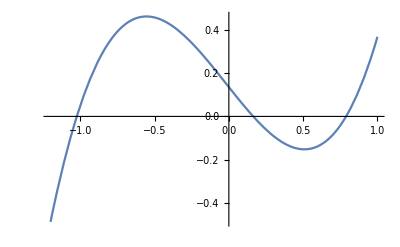

```mathematica
s1=FindRoot[E^(x-2)+x^3-x,{{x,-1}}];
s2=FindRoot[E^(x-2)+x^3-x,{{x,0}}];
s3=FindRoot[E^(x-2)+x^3-x,{{x,1}}];
s={s1,s2,s3}
Plot[E^(x-2)+x^3-x==0,{x,-1.2,1}]
```

1/2 (-ⅇ^(-2+x)+3 x-x^3)

{-0.0955895,1.38003,0.417416}

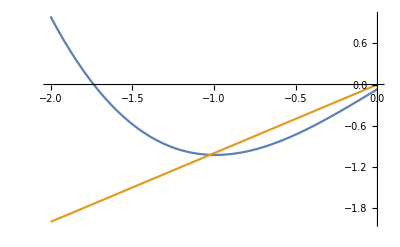

```mathematica
g1[x_]=(E^(x-2)+x^3-3x)/(-2)
g1'[x/.s]
Plot[{g1[x],x},{x,-2,0}]
```

ⅇ^(-2+x)+x^3

{3.19118,0.239939,2.16517}

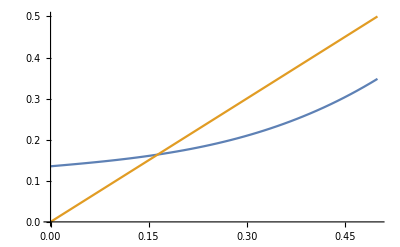

```mathematica
g2[x_]=E^(x-2)+x^3
g2'[x/.s]
Plot[{g2[x],x},{x,0,0.5}]
```

(-ⅇ^(-2+x)+x)^(1/3)

{-0.151369-0.262179 ⅈ,10.4402,0.37601}

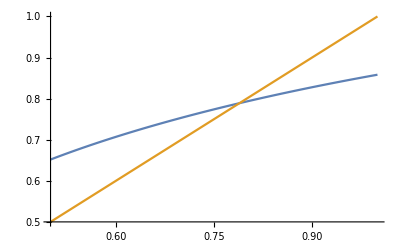

```mathematica
g3[x_]=(x-E^(x-2))^(1/3)
g3'[x/.s]
Plot[{g3[x],x},{x,0.5,1}]
```